```mathematica
NS["maxent_binomial_approx","C:\\Users\\pglpm\\repositories\\maxNt\\scripts"]
```

```mathematica
const=Integrate[Exp[-x^2/2],{x,0,1}]
```

√(π/2) Erf[1/(√2)]

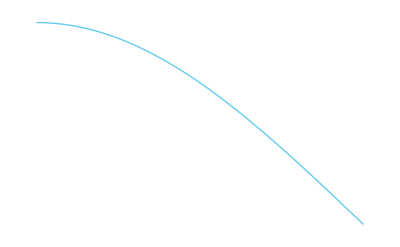

```mathematica
Plot[Exp[-x^2/2]/const,{x,0,1},PlotRange->All]
```

```mathematica
Integrate[Exp[-x^2/2+a*x+b*x^2]/const,{x,0,1}]
```

(ⅇ^(a^2/(2-4 b)) (-Erfi[a/(√(-2+4 b))]+Erfi[(-1+a+2 b)/(√(-2+4 b))]))/(√(-1+2 b) Erf[1/(√2)])

```mathematica
(* hypergeometric distribution for sample given population *)

Clear[condp2];condp2[n_,a_,nn_,aa_]:=(N@Binomial[n,a]*N@Binomial[nn-n,aa-a]/N@Binomial[nn,aa])
```

```mathematica
Clear[condp];condp[n_,a_,nn_,aa_]:=(Binomial[n,a]*Binomial[nn-n,aa-a]/Binomial[nn,aa]//N)
```

```mathematica
condb[n_,a_,an_]=Assuming[0<a<n&&0<an<1,FS@PDF[BinomialDistribution[n,an],a]]
```

(1-an)^(-a+n) an^a Binomial[n,a]

```mathematica
Sum[condb[n,a,an],{a,0,n}]
```

1

```mathematica
prior[p_]=2*(1-p)
```

2 (1-p)

```mathematica
priorn[n_,a_]=Assuming[0<a<n&&Element[a,Integers]&&Element[n,Integers],FS@Integrate[condb[n,a,an]*prior[an],{an,0,1},Assumptions->0<a<n]]
```

(2 (1-a+n) n!)/Gamma[3+n]

```mathematica
priorn[n_,a_]=2*(1-a+n)/((n+2)*(n+1))
```

(2 (1-a+n))/((1+n) (2+n))

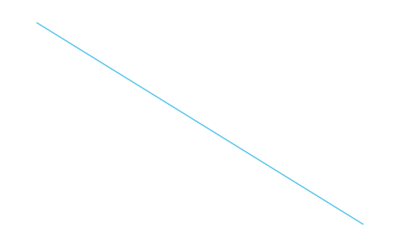

```mathematica
Plot[priorn[30,a],{a,0,30},PlotRange->{0,All}]
```

```mathematica
nx=5000;
normz1=2^nx;
normz2=1;
```

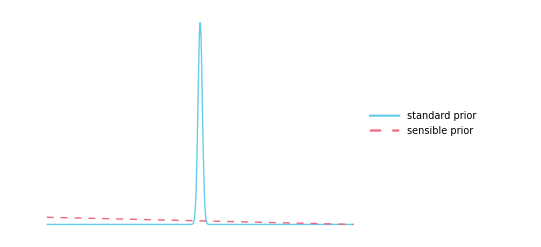

```mathematica
Plot[{Binomial[nx,a]/normz1,priorn[nx,a]},{a,0,nx},PlotRange->{All,All},PlotLegends->Placed[{"standard prior", "sensible prior"},{Left,Top}]]
```

```mathematica
expng["priors_comparison",%]
```

priors_comparison.png

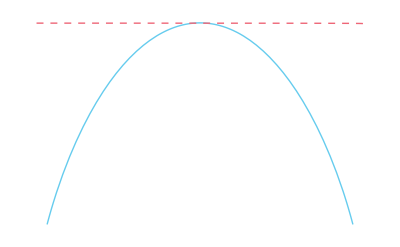

```mathematica
LogPlot[{Binomial[nx,a]/normz1,priorn[nx,a]},{a,0,nx},PlotRange->{0,All}]
```